## II. Eigenvalue analysis and analytical solution (not using Cholesky)

```mathematica
Alpha1=100; Alpha2=0;
B1=1; H=.7; B2=.1; eA= 2 10^7;
Alpha=100; roA=1; Bet=100;
L1=Sqrt[B1^2 + H^2]; L2= Sqrt[B2^2 + H^2];
r=eA H^3/ ( 3 Sqrt[3] L1^3);
```

```mathematica
MS[Alpha_,Bet_,Alpha1_,Alpha2_,Lam_]:=Module[{M,K,DD,R,U},
M= roA/3 {{L1+Bet L2,0},{0,L1}};
K=eA/L1^3 {{B1^2 + Alpha L1^3 B2^2 /L2^3, -B1 H},{-B1 H, H^2}};
DD=Alpha1 M + Alpha2 K;
R=Lam{{0},{-r}};
U=LinearSolve[K,R];
{M,K,DD,R,U}]
```

#### 1. EigenValues and EigenVectors

```mathematica
Eigen[Alpha_,Bet_,Alpha1_,Alpha2_,Lam_]:=Module[{Eigensys,EiVals,EiVecs,T,w},
Eigensys=Eigensystem[{MS[Alpha,Bet,Alpha1,Alpha2,Lam][[2]],MS[Alpha,Bet,Alpha1,Alpha2,Lam][[1]]}];
EiVals={Eigensys[[1,2]],Eigensys[[1,1]]};
EiVecs={-Eigensys[[2,2]],Eigensys[[2,1]]};
w=Sqrt[EiVals];
T=2 Pi/w;
{EiVals,EiVecs,T,w}]
```

```mathematica
Print["Eigenvalue 1 = ",Eigen[100,100,0,0,-1][[1,1]]//MatrixForm];
Print["Eigenvalue 2 =  ",Eigen[100,100,0,0,-1][[1,2]]//MatrixForm];
Print["Eigenvector 1 =  ",Eigen[100,100,0,0,-1][[2,1]]//MatrixForm];
Print["Eigenvector 2 =  ",Eigen[100,100,0,0,-1][[2,1]]//MatrixForm];
```

Eigenvalue 1 = 2.26466×10^6

Eigenvalue 2 =  1.37959×10^7

Eigenvector 1 =  (0.501906
0.864922)

Eigenvector 2 =  (0.501906
0.864922)

#### 2. Modal Matrix

```mathematica
ModT[Alpha_,Bet_,Alpha1_,Alpha2_,Lam_]:=Module[{M,K,DD,Mbar,Kbar,DDbar,Th,Kdiag,Mdiag,Ddiag},
M= MS[Alpha,Bet,Alpha1,Alpha2,Lam][[1]];
K=MS[Alpha,Bet,Alpha1,Alpha2,Lam][[2]];
DD=MS[Alpha,Bet,Alpha1,Alpha2,Lam][[3]];
Th=Transpose[Eigen[Alpha,Bet,Alpha1,Alpha2,Lam][[2]]];
Mbar=Transpose[Th] .M.Th;
Kbar=Transpose[Th] .K.Th;
DDbar=Transpose[Th] .DD.Th;
Kdiag=Diagonal[Kbar];
Mdiag=Diagonal[Mbar];
Ddiag=Diagonal[DDbar];
{Kdiag,Mdiag,Ddiag,Th}]
```

```mathematica
Print["Modal Matrix = [Eigenvector1 Eigenvector2]= ",ModT[100,100,0,0,-1][[4]]//MatrixForm]
Print["K_diag = ",ModT[100,100,0,0,-1][[1]]//MatrixForm]
Print["M_diag = ",ModT[100,100,0,0,-1][[2]]//MatrixForm]
Print["D_diag = ",ModT[100,100,0,0,-1][[3]]//MatrixForm]
```

Modal Matrix = [Eigenvector1 Eigenvector2]= (0.501906 | -0.029231
0.864922 | 0.999573)

K_diag = (1.43681×10^7
5.89118×10^6)

M_diag = (6.34446
0.427025)

D_diag = (0.
0.)

#### 3. Routine for analytical solution ( free motion ) Lamda=-1

```mathematica
uvana[Alpha_,Bet_,Alpha1_,Alpha2_,Lam_,t_]:=Module[{w,Si,wD,u0Bar,v0Bar,uBar,vBar,aBar,ua,va,aa},
w=Eigen[Alpha,Bet,Alpha1,Alpha2,Lam][[4]];
Si=ModT[Alpha,Bet,Alpha1,Alpha2,Lam][[3]]/(2 w ModT[Alpha,Bet,Alpha1,Alpha2,Lam][[2]]);
wD=w Sqrt[1-Si^2];
u0Bar=Inverse[ModT[Alpha,Bet,Alpha1,Alpha2,Lam][[4]]].MS[Alpha,Bet,Alpha1,Alpha2,Lam][[5]];
v0Bar=0;
uBar=Exp[-Si w t] (u0Bar Cos[wD t] + (v0Bar + Si w u0Bar)/(wD) Sin[wD t]);
vBar=1/wD ⅇ^(-Si t w) (v0Bar wD Cos[t wD]-(Si v0Bar w+Si^2 u0Bar w^2+u0Bar wD^2) Sin[t wD]);
aBar=1/wD ⅇ^(-Si t w) (-wD (2 Si v0Bar w+Si^2 u0Bar w^2+u0Bar wD^2) Cos[t wD]+(Si^2 v0Bar w^2+Si^3 u0Bar w^3-v0Bar wD^2+Si u0Bar w wD^2) Sin[t wD]);
ua=ModT[Alpha,Bet,Alpha1,Alpha2,Lam][[4]].uBar;
va=ModT[Alpha,Bet,Alpha1,Alpha2,Lam][[4]].vBar;
aa=ModT[Alpha,Bet,Alpha1,Alpha2,Lam][[4]].aBar;
{ua,va,aa}]
```

```mathematica
PlotPhase[Alpha_,Bet_,Alpha1_,Alpha2_,Lam_,tf_]:=Module[{gra1,gra2,pha1,pha2},
gra1=Plot[uvana[Alpha,Bet,Alpha1,Alpha2,Lam,t][[1,1]]/B2,{t,0,tf},Frame->True,FrameLabel->{"t[s]","u_1/B2"}];
gra2=Plot[uvana[Alpha,Bet,Alpha1,Alpha2,Lam,t][[1,2]]/H,{t,0,tf},Frame->True,FrameLabel->{"t[s]","u_2/H"}];
pha1=ParametricPlot[Flatten[{uvana[Alpha,Bet,Alpha1,Alpha2,Lam,t][[1,1]]/B2,uvana[Alpha,Bet,Alpha1,Alpha2,Lam,t][[2,1]] Eigen[Alpha,Bet,Alpha1,Alpha2,Lam][[3,1]]/B2}],{t,0,tf},Frame->True,FrameLabel->{"u_1/B2","((u̇)_1)/B2"},PlotRange->Full, AspectRatio->1];
pha2=ParametricPlot[Flatten[{uvana[Alpha,Bet,Alpha1,Alpha2,Lam,t][[1,2]]/B2,uvana[Alpha,Bet,Alpha1,Alpha2,Lam,t][[2,2]] Eigen[Alpha,Bet,Alpha1,Alpha2,Lam][[3,2]]/B2}],{t,0,tf},Frame->True,FrameLabel->{"u_2/B2","((u̇)_2)/B2"},PlotRange->Full, AspectRatio->1];
{gra1,gra2,pha1,pha2}
]
```

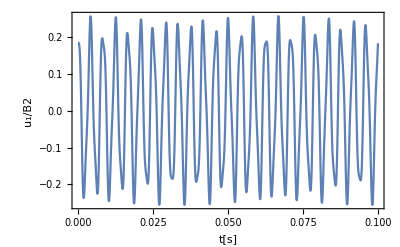
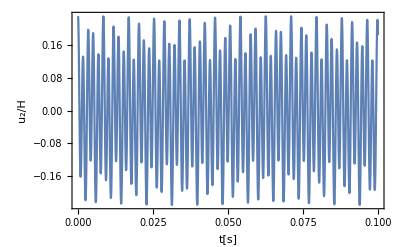
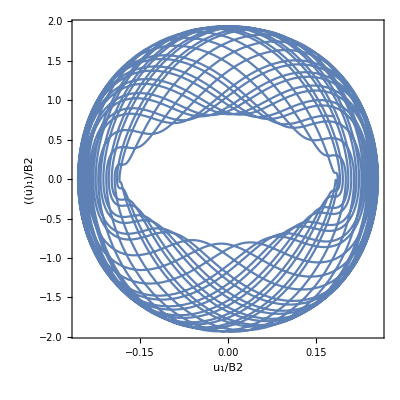
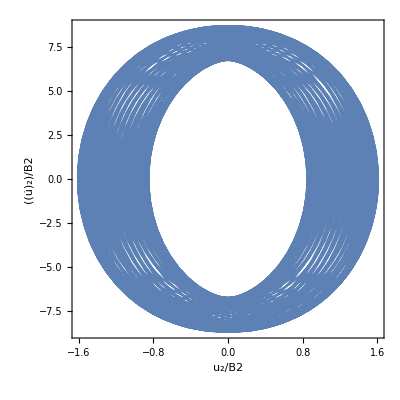

```mathematica
(* Case 1: Beta =100; Alpha1=0; Alpha2=0; Lamda=-1 *)
PlotPhase[100,100,0,0,-1,0.1]
```

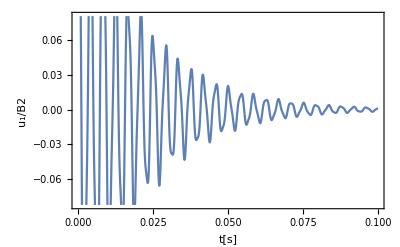
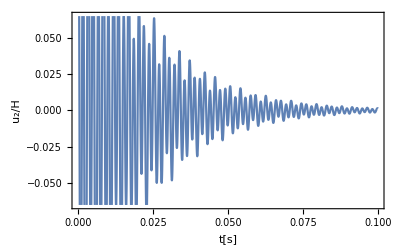
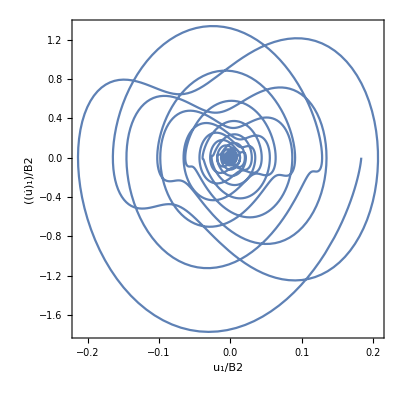
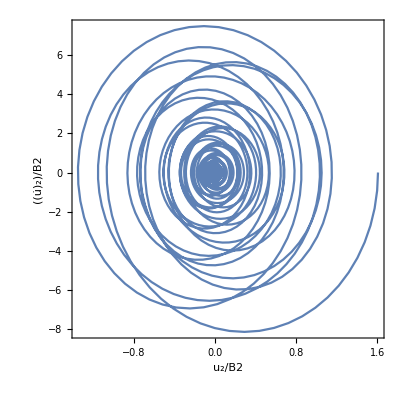

```mathematica
(* Case 2: Beta =100; Alpha1=100; Alpha2=0; Lamda=-1 *)
PlotPhase[100,100,100,0,-1,0.1]
```

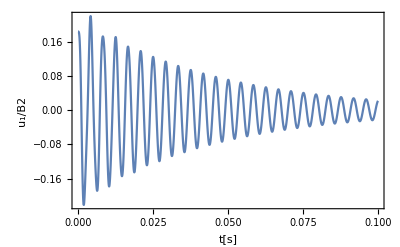
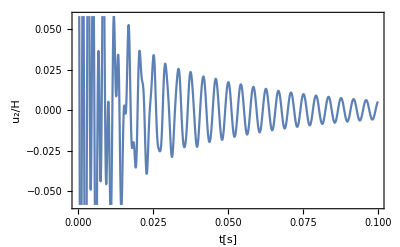
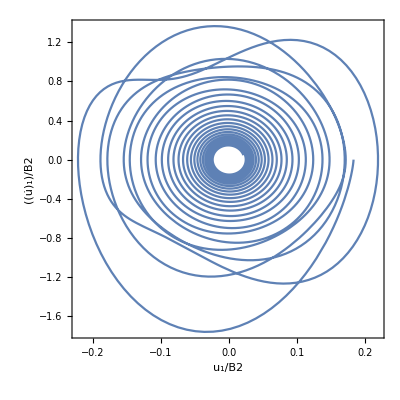
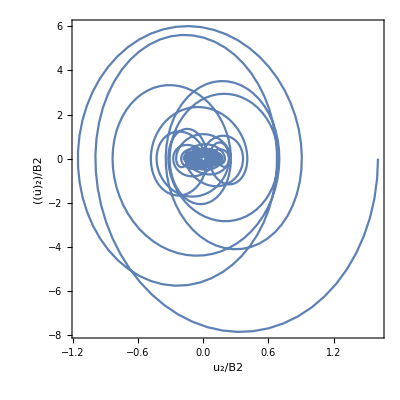

```mathematica
(* Case 3: Beta =100; Alpha1=0; Alpha2=2 10^(-5); Lamda=-1 *)
PlotPhase[100,100,0,2 10^(-5),-1,0.1]
```

#### 4. Study of different parameter combinations

```mathematica
In1={100,100,0,0,(Eigen[Alpha,#,0,0,-1][[4,2]])/(Eigen[Alpha,#,0,0,-1][[4,1]])}&/@{100};
In2={100,100,100,0,(Eigen[Alpha,#,100,0,-1][[4,2]])/(Eigen[Alpha,#,100,0,-1][[4,1]])}&/@{100};
In3={100,100,0,500,(Eigen[Alpha,#,0,500,-1][[4,2]])/(Eigen[Alpha,#,0,500,-1][[4,1]])}&/@{100};
In4={100,100,100,500,(Eigen[Alpha,#,100,500,-1][[4,2]])/(Eigen[Alpha,#,100,500,-1][[4,1]])}&/@{100};
TableForm[Join[In1,In2,In3,In4],TableHeadings->{None,{α,β,Subscript[α, 1],Subscript[α, 2],Subscript[ω, 2]/Subscript[ω, 1]}}]
```

α | β | α_1 | α_2 | ω_2/ω_1
100 | 100 | 0 | 0 | 2.46816
100 | 100 | 100 | 0 | 2.46816
100 | 100 | 0 | 500 | 2.46816
100 | 100 | 100 | 500 | 2.46816